## Bh and NoBh Region for (α and Q space time parameters)

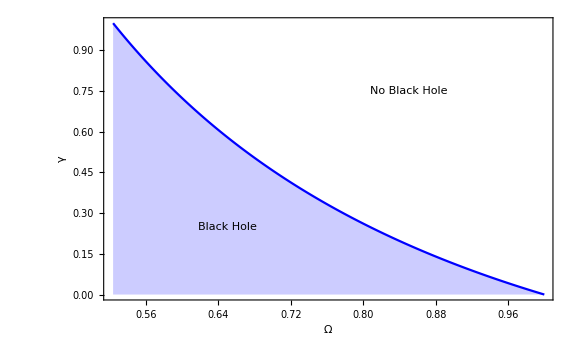

```mathematica
f[r_,Ω_,γ_] = 1-2/r(1+Ω/r^2+(Ω*γ)/r^3)^-1;
gg=Table[γ,{γ,0.,1,0.001}];
OO = Table[Ω/.FindRoot[{(f[r,Ω,γ]/.{γ->gg[[i]]})==0,D[(f[r,Ω,γ]/.{γ->gg[[i]]}),r]==0},{{r,1},{Ω,1}}],{i,1,Length[gg]}];
OOgg = Table[{OO[[i]],gg[[i]]},{i,1,Length[gg]}];

ListLinePlot[OOgg,Frame->True,FrameLabel->{"Ω","γ"},Filling->Axis,LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black],PlotRange->{{0.5229,1},{0,1}},PlotStyle->Blue,BaseStyle->{14,FontFamily->"Times"},
Epilog->{Text[Rotate[Framed["Black Hole",FrameStyle->None,Background->None],0Degree],{0.65,0.25}],Text[Rotate[Framed["No Black Hole",FrameStyle->None,Background->None],0Degree],{0.85,0.75}]},ImageSize->Large]
```

```mathematica
Ω/.FindRoot[{(f[r,Ω,γ]/.{γ->0.5})==0,D[(f[r,Ω,γ]/.{γ->0.5}),r]==0},{{r,1.94},{Ω,1}}];
γ/.FindRoot[{(f[r,Ω,γ]/.{Ω->0.7})==0,D[(f[r,Ω,γ]/.{Ω->0.7}),r]==0},{{r,1.94},{γ,1}}];
FindRoot[f[r,0.56,0.87]==0,{r,1}]
(*Ajoyib natijalar*)
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{r→1.17783}

## lapse function

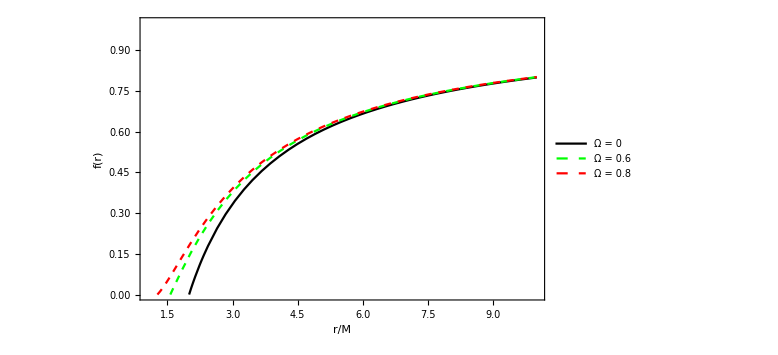

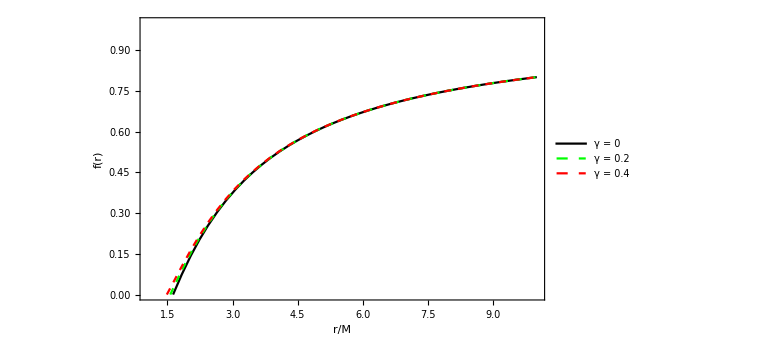

{r→1.48865}

```mathematica
f[r_,Ω_,γ_] = 1-2(*M*)/r(1+(Ω (*M^2*))/r^2+(Ω*γ (*M^3*))/r^3)^-1;
Plot[{f[r,0.,0.2],f[r,0.6,0.2],f[r,0.8,0.2]},{r,0,10},PlotRange->{{1.0514,10},{0,1}},Frame->True,FrameLabel->{"r/M","f(r)","γ=0.2"},ImageSize->Large,PlotStyle-> {{Black},{Dashed,Green},{Dashed,Red}},PlotLegends->Placed[{"Ω = 0","Ω = 0.6","Ω = 0.8"},{Scaled[{0.60,0.5}],{0,0.5}}],LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]


Plot[{f[r,0.6,0.],f[r,0.6,0.2],f[r,0.6,0.4]},{r,0,10},PlotRange->{{1.0514,10},{0,1}},Frame->True,FrameLabel->{"r/M","f(r)","Ω=0.6"},ImageSize->Large,PlotStyle-> {{Black},{Dashed,Green},{Dashed,Red}},PlotLegends->Placed[{"γ = 0","γ = 0.2","γ = 0.4"},{Scaled[{0.60,0.5}],{0,0.5}}],LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]

FindRoot[f[r,0.6,0.4]==0,{r,2}](*Last command for getting event horizon radii*)
```

## Event Horizon Radii

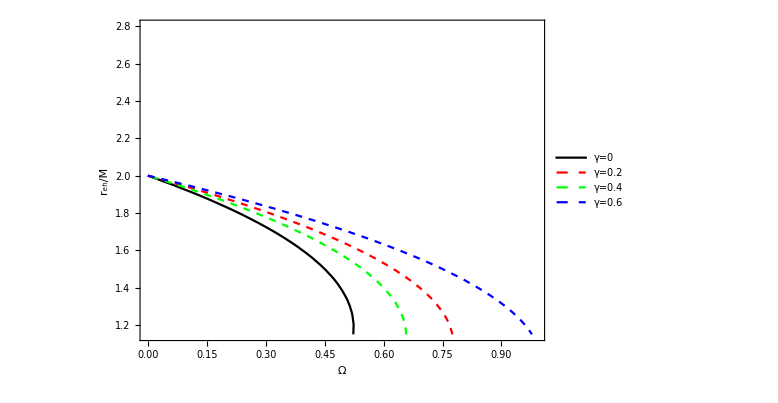

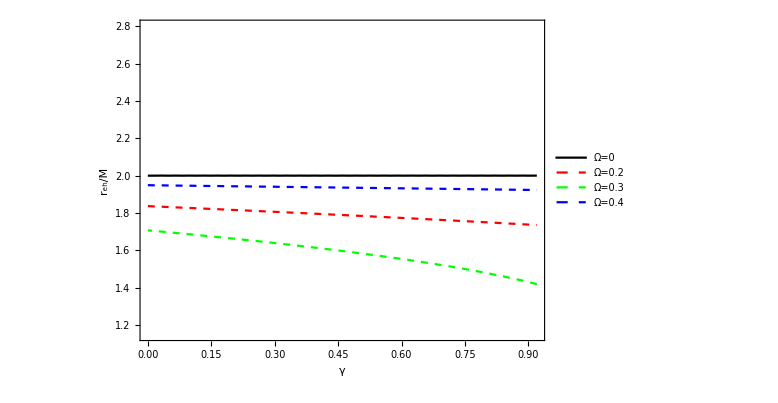

```mathematica
f[r_,Ω_,γ_] = 1-2/r(1+Ω/r^2+(Ω*γ)/r^3)^-1;

ContourPlot[{f[r,Ω,1]==0,f[r,Ω,0.3]==0,f[r,Ω,0.56]==0,f[r,Ω,0.]==0},{Ω,0.,0.99},{r,1.15,2.8},ContourStyle->{{Black},{Dashed,Red},{Dashed,Green},{Dashed,Blue}},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},FrameLabel->{"Ω","r_eh/M"},PlotLegends->Placed[{"γ=0","γ=0.2","γ=0.4","γ=0.6"},{Scaled[{0.60,0.7}],{0,0.5}}],ImageSize->Large](* ! ! ! γ fixed for event horizon radii plot*)
ContourPlot[{f[r,0.,γ]==0,f[r,0.3,γ]==0,f[r,0.5,γ]==0,f[r,0.1,γ]==0},{γ,0,0.92},{r,1.15,2.8},ContourStyle->{{Black},{Dashed,Red},{Dashed,Green},{Dashed,Blue}},AspectRatio->0.7,Frame->True,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},FrameLabel->{"γ","r_eh/M"},PlotLegends->Placed[{"Ω=0","Ω=0.2","Ω=0.3","Ω=0.4"},{Scaled[{0.62,0.73}],{0,0.5}}],ImageSize->Large]
FindRoot[f[r,0.,0]==0,{r,1}];
```

## Angular momentum and energy

### Angular momentum

{{r→-0.336497},{r→5.16971}}

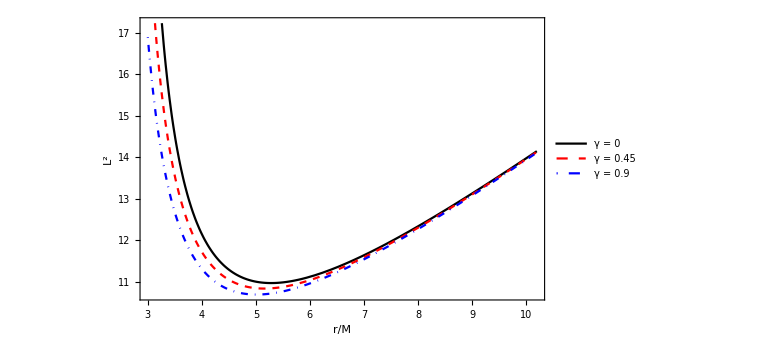

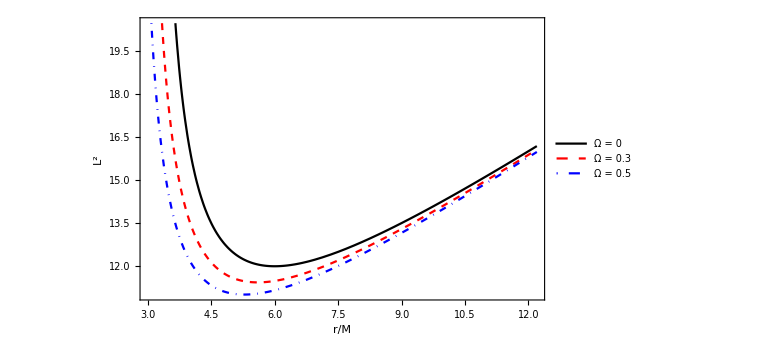

```mathematica
L[r_,Ω_,γ_] = ((2 f[r,Ω,γ])/(D[f[r,Ω,γ],r] r^3) - 1/r^2)^-0.5;//Simplify
NSolve[D[L[r,0.6,0.4],r] == 0,Reals](*ISCO uchun ham o'rinli bo'ladi r - 6. *)
Plot[{L[r,0.6,0]^2,L[r,0.6,0.45]^2,L[r,0.6,0.9]^2},{r,3,10.2},ImageSize->Large,Frame->True,FrameLabel->{"r/M","L^2","Ω=0.6"} ,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotStyle->{{Black},{Dashed,Red},{DotDashed,Blue}},PlotLegends->Placed[{"γ = 0"," γ = 0.45"," γ = 0.9"},{Scaled[{0.2,0.25}],{-2,-1.5}}]]

 
Plot[{L[r,0.,0.6]^2,L[r,0.3,0.6]^2,L[r,0.5,0.6]^2},{r,3,12.2},ImageSize->Large,Frame->True,FrameLabel->{"r/M","L^2","γ=0.6"} ,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotStyle->{{Black},{Dashed,Red},{DotDashed,Blue}},PlotLegends->Placed[{"Ω = 0"," Ω = 0.3"," Ω = 0.5"},{Scaled[{0.2,0.25}],{-2,-1.5}}]]
```

### Energy

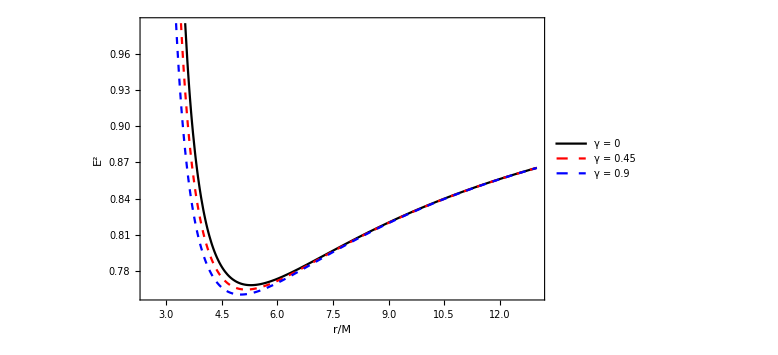

```mathematica
Ene[r_,Ω_,γ_] = ((√(1/r))/(√((-3 r^5+r^6+2 r^4 Ω+r^3 (-1+2 γ) Ω+r^2 Ω^2+2 r γ Ω^2+γ^2 Ω^2)/(r (-2 r^2+r^3+r Ω+γ Ω)^2))))^2;
Plot[{Ene[r,0.6,0]^2,Ene[r,0.6,0.45]^2,Ene[r,0.6,0.9]^2},{r,2.5,13},ImageSize->Large,Frame->True,FrameLabel->{"r/M","E^2","Ω=0.6"} ,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotStyle->{{Black},{Dashed,Red},{Dashed,Blue}},PlotLegends->Placed[{"γ = 0"," γ = 0.45"," γ = 0.9"},{Scaled[{0.2,0.25}],{-2,-1.5}}]]
Plot[{Ene[r,0.,0.6]^2,Ene[r,0.45,0.6]^2,Ene[r,0.6,0.9]^2},{r,3,12.2},ImageSize->Large,Frame->True,FrameLabel->{"r/M","E^2","γ=0.6"} ,LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotStyle->{{Black},{Dashed,Red},{DotDashed,Blue}},PlotLegends->Placed[{"Ω = 0"," Ω = 0.45"," Ω = 0.9"},{Scaled[{0.2,0.25}],{-2,-1.5}}]]
```

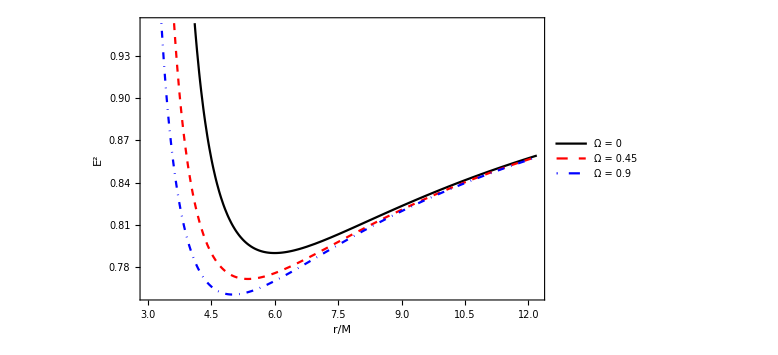

## Effective Potential

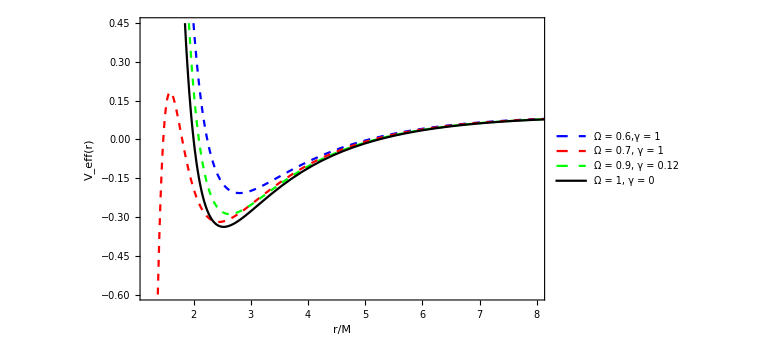

```mathematica
f[r_,Ω_,γ_] = 1-2/r(1+Ω/r^2+(Ω*γ)/r^3)^-1;
Veff[Ene_,L_,r_,Ω_,γ_]=-1 + Ene^2/f[r,Ω,γ]-L^2/r^2;
Plot[{Veff[1,4,r,0.6,1],Veff[1,4,r,0.7,1],Veff[1,4,r,0.9,0.12],Veff[1,4,r,1,0]},{r,1.2,10},PlotRange->{{1.2,8},{-0.6,0.45}},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=4"},Frame->True,LabelStyle->Directive[FontFamily->"Times",FontSize->14,Black, Italic,FontColor->Black],PlotLegends->Placed[{"Ω = 0.6,γ = 1","Ω = 0.7, γ = 1","Ω = 0.9, γ = 0.12","Ω = 1, γ = 0"},{Scaled[{0.08,0.35}],{-1.9,0.5}}],PlotStyle->{{Dashed,Blue},{Dashed,Red},{Dashed,Green},{Black}},ImageSize->Large]
```

## ISCO radius

### ISCO calcuations

```mathematica
f[r_,Ω_,γ_] = 1-2/r(1+Ω/r^2+(Ω*γ)/r^3)^-1;
Veff[Ene_,L_,r_,Ω_,γ_]=-1 + Ene^2/f[r,Ω,γ]-L^2/r^2;
DDVeff[Ene_,L_,r_,Ω_,γ_] = (-2 Ene^2 D[D[f[r,Ω,γ],r],r])/(f[r,Ω,γ]*f[r,Ω,γ]) + (2 Ene^2 (D[f[r,Ω,γ],r])^2)/(f[r,Ω,γ])^3 - (6 L^2)/r^4;(*Second order derrivative from Veff*)
NSolve[DDVeff[1,4,r,0.,0]==0,r,Reals];
D[D[f[r,Ω,γ],r],r];
Solve[Veff[Ene,L,r,Ω,γ]==0 ,L];
Solve[(D[Veff[Ene,L,r,Ω,γ],r]/.{L->(r √(2 r^2-r^3+Ene^2 r^3-r Ω+Ene^2 r Ω-γ Ω+Ene^2 γ Ω))/(√(-2 r^2+r^3+r Ω+γ Ω))})==0,Ene];
D[Veff[Ene,L,r,Ω,γ],r]/.{L->(r √(2 r^2-r^3+Ene^2 r^3-r Ω+Ene^2 r Ω-γ Ω+Ene^2 γ Ω))/(√(-2 r^2+r^3+r Ω+γ Ω))};//Simplify
Ene[r_,Ω_,γ_] = (√(1/r))/(√((-3 r^5+r^6+2 r^4 Ω+r^3 (-1+2 γ) Ω+r^2 Ω^2+2 r γ Ω^2+γ^2 Ω^2)/(r (-2 r^2+r^3+r Ω+γ Ω)^2)));
D[Ene[r,0,0],r];//Simplify (*dE/dr = 0 for ISCO radii*)
NSolve[D[Ene[r,0.,0.],r]==0,r,Reals] (*This expression can catch ISCO radius, that is Subscript[r, ISCO] -> 6 when Ω and γ space-time parameters will get zero simultenously ! ! ! *)
```

{{r→6.}}

### ISCO plots

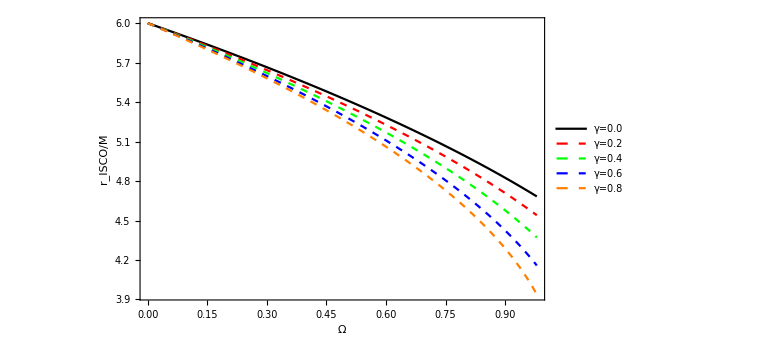

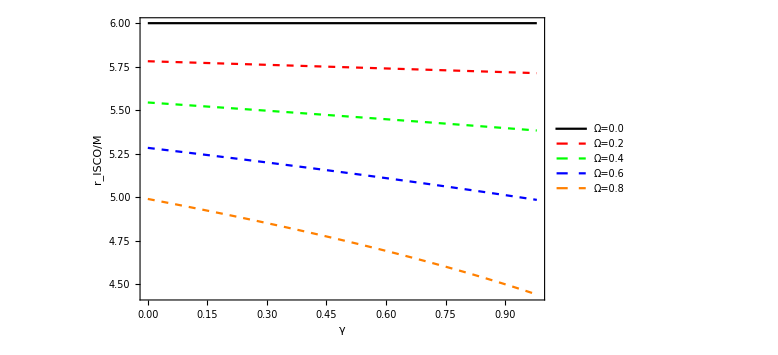

```mathematica
rr[Ω_,γ_]:=r/.FindRoot[D[Ene[r,Ω,γ],r]==0,{r,5.}];
Plot[{rr[Ω,0],rr[Ω,0.2],rr[Ω,0.4],rr[Ω,0.6],rr[Ω,0.75]},{Ω,0.,0.98},Frame->True,FrameLabel->{"Ω","r_ISCO/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"γ=0.0","γ=0.2","γ=0.4","γ=0.6","γ=0.8"},{Scaled[{0.60,0.7}],{-0.8,0.3}}],PlotStyle->{{Black},{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed, Orange}},ImageSize->Large]
Plot[{rr[0,γ],rr[0.2,γ],rr[0.4,γ],rr[0.6,γ],rr[0.8,γ]},{γ,0.,0.98},Frame->True,FrameLabel->{"γ","r_ISCO/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"Ω=0.0","Ω=0.2","Ω=0.4","Ω=0.6","Ω=0.8"},{Scaled[{0.60,0.7}],{-0.1,1}}],PlotStyle->{{Black},{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed,Orange}},ImageSize->Large]
```